```mathematica
K[x]=Exp[-1/(1-x^2)]
```

ⅇ^(-1/(1-x^2))

General::munfl: Exp[-12238.] is too small to represent as a normalized machine number; precision may be lost.

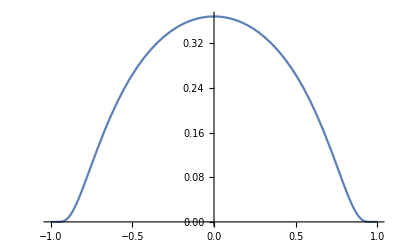

```mathematica
Plot[ⅇ^(-1/(1-x^2)),{x,-1,1}]
```

```mathematica
F[x]=a*Exp[-a*x]
```

a ⅇ^(-a x)

```mathematica
pp[x1_,x2_,x3_]=a1*a2*a3*Exp[-a1*x1-a2*x2-a3*x3]
```

a1 a2 a3 ⅇ^(-a1 x1-a2 x2-a3 x3)

```mathematica
pp
```

pp

```mathematica
pp[1,2,3]
```

a1 a2 a3 ⅇ^(-a1-2 a2-3 a3)

```mathematica
Integrate[pp[x1,x2,x3],{x1,0,x2}]
```

```mathematica
a2 a3 ⅇ^(-a1 x2-a2 x2-a3 x3) (-1+ⅇ^(a1 x2))
Simplify[%]
```

a2 a3 ⅇ^(-a1 x2-a2 x2-a3 x3) (-1+ⅇ^(a1 x2))

a2 a3 ⅇ^(-a1 x2-a2 x2-a3 x3) (-1+ⅇ^(a1 x2))

```mathematica
pp3[x2_,x3_]=a2 a3 ⅇ^(-a1 x2-a2 x2-a3 x3) (-1+ⅇ^(a1 x2))
```

a2 a3 ⅇ^(-a1 x2-a2 x2-a3 x3) (-1+ⅇ^(a1 x2))

```mathematica
pp3[2,3]
```

a2 a3 ⅇ^(-2 a1-2 a2-3 a3) (-1+ⅇ^(2 a1))

```mathematica
Integrate[pp3[x2,x3],{x2,0,x3}]
a3 ⅇ^(-(a2+a3) x3) (-1+ⅇ^(a2 x3))-(a2 a3 ⅇ^(-(a1+a2+a3) x3) (-1+ⅇ^((a1+a2) x3)))/(a1+a2)
```

a3 ⅇ^(-(a2+a3) x3) (-1+ⅇ^(a2 x3))-(a2 a3 ⅇ^(-(a1+a2+a3) x3) (-1+ⅇ^((a1+a2) x3)))/(a1+a2)

a3 ⅇ^((-a2-a3) x3) (-1+ⅇ^(a2 x3))-(a2 a3 ⅇ^((-a1-a2-a3) x3) (-1+ⅇ^((a1+a2) x3)))/(a1+a2)

```mathematica
Simplify[a3 ⅇ^((-a2-a3) x3) (-1+ⅇ^(a2 x3))-(a2 a3 ⅇ^((-a1-a2-a3) x3) (-1+ⅇ^((a1+a2) x3)))/(a1+a2)]
```

a3 ⅇ^(-(a2+a3) x3) (-1+ⅇ^(a2 x3))-(a2 a3 ⅇ^(-(a1+a2+a3) x3) (-1+ⅇ^((a1+a2) x3)))/(a1+a2)

```mathematica
a3 ⅇ^(-(a2+a3) x3) (-1+ⅇ^(a2 x3))-(a2 a3 ⅇ^(-(a1+a2+a3) x3) (-1+ⅇ^((a1+a2) x3)))/(a1+a2)
pp4[x3_]=a3 ⅇ^(-(a2+a3) x3) (-1+ⅇ^(a2 x3))-(a2 a3 ⅇ^(-(a1+a2+a3) x3) (-1+ⅇ^((a1+a2) x3)))/(a1+a2)
pp4
```

a3 ⅇ^((-a2-a3) x3) (-1+ⅇ^(a2 x3))-(a2 a3 ⅇ^((-a1-a2-a3) x3) (-1+ⅇ^((a1+a2) x3)))/(a1+a2)

a3 ⅇ^((-a2-a3) x3) (-1+ⅇ^(a2 x3))-(a2 a3 ⅇ^((-a1-a2-a3) x3) (-1+ⅇ^((a1+a2) x3)))/(a1+a2)

pp4

```mathematica
Integrate[pp4[x3],{x3,0,Infinity}]
```

```mathematica
ConditionalExpression[(a1 a2)/((a2+a3) (a1+a2+a3)),Re[a3]>0&&Re[a2+a3]>0&&Re[a1+a2+a3]>0]
Problem1[a1_,a2_,a3_]=(a1 a2)/((a2+a3) (a1+a2+a3))
Problem1[1,2,3]
```

ConditionalExpression[(a1 a2)/((a2+a3) (a1+a2+a3)),Re[a3]>0&&Re[a2+a3]>0&&Re[a1+a2+a3]>0]

(a1 a2)/((a2+a3) (a1+a2+a3))

1/15

```mathematica
N[1/15]
```

0.0666667

```mathematica
pp2[2,3]
```

(a1 a2 a3 ⅇ^(-3 (x2+x3)) (-1+ⅇ^x2))[2,3]

```mathematica
Integrate[pp2[x2,x3],{x2,0,x3}]
```

∫_0^x3 (a1 a2 a3 ⅇ^(-3 (x2+x3)) (-1+ⅇ^x2))[x2,x3]ⅆx2

```mathematica
Integrate[p[x1,x2,x3],{x1,0,x2}]
```

a2 a3 ⅇ^(-a1 x2-a2 x2-a3 x3) (-1+ⅇ^(a1 x2))

```mathematica
Integrate[p[x1,x2,x3],{x1,0,x2},{x2,0,x3},{x3,0,Infinity}]
```

ⅇ^(-a1 x2-a2 x3) (-1+ⅇ^(a1 x2)) (-1+ⅇ^(a2 x3))

```mathematica
Simplify[1-ⅇ^(-a1 x2)-ⅇ^(-a2 x3)+ⅇ^(-a1 x2-a2 x3)]
```

ⅇ^(-a1 x2-a2 x3) (-1+ⅇ^(a1 x2)) (-1+ⅇ^(a2 x3))

```mathematica
p1=%
```

a2 a3 ⅇ^(-(a1+a2) x2-a3 x3) (-1+ⅇ^(a1 x2))

```mathematica
Assuming[{{a2>0},{a3>0}},Integrate[p1[x2,x3],{x2,0,x3}]]
```

∫_0^x3 (a2 a3 ⅇ^(-(a1+a2) x2-a3 x3) (-1+ⅇ^(a1 x2)))[x2,x3]ⅆx2

```mathematica
1+(x2^2+x3^2+2x2*x3+x1*x3)/((x1+x2)(x1+x2+x3))
```

1+(x2^2+x1 x3+2 x2 x3+x3^2)/((x1+x2) (x1+x2+x3))

```mathematica
Simplify[1+(x2^2+x1 x3+x1 x2 x3+x3^2)/((x1+x2) (x1+x2+x3))]
```

1+(x2^2+x1 x2 x3+x3 (x1+x3))/((x1+x2) (x1+x2+x3))

```mathematica
Expand[1+(x2^2+x1 x2 x3+x3 (x1+x3))/((x1+x2) (x1+x2+x3))]
```

1+x2^2/((x1+x2) (x1+x2+x3))+(x1 x3)/((x1+x2) (x1+x2+x3))+(x1 x2 x3)/((x1+x2) (x1+x2+x3))+x3^2/((x1+x2) (x1+x2+x3))

```mathematica
Expand[1+(x2^2+2 x2 x3+x3 (x1+x3))/((x1+x2) (x1+x2+x3))]
```

1+x2^2/((x1+x2) (x1+x2+x3))+(x1 x3)/((x1+x2) (x1+x2+x3))+(2 x2 x3)/((x1+x2) (x1+x2+x3))+x3^2/((x1+x2) (x1+x2+x3))

```mathematica
KKK[x1_,x2_,x3_]=1-(x2^2+x3^2+x1*x2+x2*x3+x1*x3)/((x1+x2)(x1+x2+x3))
```

1-(x1 x2+x2^2+x1 x3+x2 x3+x3^2)/((x1+x2) (x1+x2+x3))

```mathematica
Simplify[1+(x1 x2+x2^2+x1 x3+x2 x3+x3^2)/((x1+x2) (x1+x2+x3))]
```

1+(x2^2+x2 x3+x3^2+x1 (x2+x3))/((x1+x2) (x1+x2+x3))

```mathematica
R[1,2,3]
```

```mathematica
R[1,2,3]
```

R[1,2,3]

```mathematica
R[{1,2,3}]
```

R[{1,2,3}]

```mathematica
KKK[1,2,3]
```

```mathematica
KKK[1,2,3]
```

-1/3

```mathematica
KK[x_,y_,z_]=1-z/(x+y)-y/(x+y)+z*y/((x+y)*(x+y+z))
```

1-y/(x+y)-z/(x+y)+(y z)/((x+y) (x+y+z))

```mathematica
KK[1,2,3]
```

-1/3

```mathematica
pp5[x1_,x2_,x3_]=(x1+x3)/(x1+x2+x3)
```

(x1+x3)/(x1+x2+x3)

```mathematica
pp5[1,2,3]
```

2/3

```mathematica
N[2/3]
```

0.666667

```mathematica
pp4
```

pp4

```mathematica
Problem1[5,3,8]
```

15/176

```mathematica
N[15/176]
```

0.0852273

```mathematica
Problem1[1,2,3]
```

1/15

```mathematica
N[1/15]
```

0.0666667

```mathematica
2/(2+3)
```

2/5

```mathematica
N[2/5]
```

0.4

```mathematica
f[x_]=a3(1-Exp[-a1*x])*(1-Exp[-a2*x])*Exp[-a3*x]
```

a3 ⅇ^(-a3 x) (1-ⅇ^(-a1 x)) (1-ⅇ^(-a2 x))

```mathematica
Integrate[f[x],{x,0,Infinity}]
```

ConditionalExpression[a3 (1/a3-1/(a1+a3)-1/(a2+a3)+1/(a1+a2+a3)),Re[a3]>0&&Re[a1+a3]>0&&Re[a2+a3]>0&&Re[a1+a2+a3]>0]

```mathematica
Problem1b[a1_,a2_,a3_]=a3 (1/a3-1/(a1+a3)-1/(a2+a3)+1/(a1+a2+a3))
```

a3 (1/a3-1/(a1+a3)-1/(a2+a3)+1/(a1+a2+a3))

```mathematica
Simplify[a3 (1/a3-1/(a1+a3)-1/(a2+a3)+1/(a1+a2+a3))]
```

(a1 a2 (a1+a2+2 a3))/((a1+a3) (a2+a3) (a1+a2+a3))

```mathematica
Problem1b[1,2,3]
```

3/20

```mathematica
N[3/20]
```

0.15

```mathematica
Problem1B[a1_,a2_,a3_]=(a1+a3)/(a1+a2+2a3)
```

(a1+a3)/(a1+a2+2 a3)

```mathematica
Problem1B[1,2,3]
```

4/9

```mathematica
N[4/9]
```

0.444444

```mathematica
1-Exp[-1*0.2](2)/(1+2)
```

0.454179

```mathematica
N[1-2/(3 ⅇ^3)]
```

0.966809

```mathematica
T1[t1_,t2_]=t2 a1 Exp[-a1 t1] a2 Exp[-a2 t2]
```

a1 a2 ⅇ^(-a1 t1-a2 t2) t2

```mathematica
Assuming[{a1>0,a2>0},Integrate[Integrate[T1[t1,t2],{t2,t1,Infinity}],{t1,0,Infinity}]]
```

(a1 (a1+2 a2))/(a2 (a1+a2)^2)

```mathematica
%
```

ConditionalExpression[(a1 (a1+2 a2))/(a2 (a1+a2)^2),Re[a2]>0&&Re[a1+a2]>0]

```mathematica
E21[a1_,a2_]=(a1 (a1+2 a2))/(a2 (a1+a2)^2)
```

(a1 (a1+2 a2))/(a2 (a1+a2)^2)

```mathematica
E21[a1,a2]+E21[a2,a1]+1/a1 +1/a2
```

1/a1+1/a2+(a2 (2 a1+a2))/(a1 (a1+a2)^2)+(a1 (a1+2 a2))/(a2 (a1+a2)^2)

```mathematica
Simplify[1/a1+1/a2+(a2 (2 a1+a2))/(a1 (a1+a2)^2)+(a1 (a1+2 a2))/(a2 (a1+a2)^2)]
```

```mathematica
Simplify[2/a1+(1/a2)[1+a1/(a1+a2)]]
```

```mathematica
E211[a1_,a2_]=2/a1+(1/a2)[1+a1/(a1+a2)]
```

2/a1+1/a2[1+a1/(a1+a2)]

```mathematica
E211[5,7]-E21[5,7]
```

1541/5040+1/7[17/12]

```mathematica
Binomial[8,3]/(2^8)
```

7/32